## This file used to be BC_FirstTryTOSS The file is modified by Carl.

```mathematica
WantDetails="NoWantDetails"
```

NoWantDetails

## Section 1. Points on the path and points on the lattice. No elastic maps are involved.

```mathematica
ListSigmaAll={TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE};
```

#### I seem to have deleted the following paragraph and hence had to redo it, so it may be not quite what we want. But do not change it after later calculations have been made, since they would then need to be redone.

```mathematica
ww=1.;ww=1.2;
NodePt[ISO]  :={0.,5-.5};   
NodePt[XISO]:={-1ww,4.};   
NodePt[TRIG]:={-1ww,3.-.15};  (* -.15 is to discourage coincident points *)
NodePt[CUBE]:={  1ww,4.};
NodePt[TET]  :={  1ww,3.};  
NodePt[ORTH]:={  1ww,2.};  
NodePt[MONO]:={0.,1+.5};  
NodePt[TRIV]:={0.,0+.5};  
NodePts=NodePt/@ListSigmaAll
dummy;
```

{{0.,0.5},{0.,1.5},{1.2,2.},{1.2,3.},{-1.2,4.},{0.,4.5},{-1.2,2.85},{1.2,4.}}

```mathematica
xyIsNodePt[{x_,y_}]:=MemberQ[NodePts,{x,y}];   (* A statement, either true or false *)
```

#### Example

```mathematica
xyIsNodePt[{0.,1.5}]
xyIsNodePt[{0.,1.7}]
```

True

False

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{NodePt[TRIV],NodePt[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{NodePt[MONO],NodePt[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{NodePt[ORTH],NodePt[TET]},   .2]},   (* from ORTH *)
{Arrow[{NodePt[TET],  NodePt[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{NodePt[TRIG],NodePt[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{NodePt[TET],  NodePt[XISO]},.3]},   (* from TET to XISO *)
{Arrow[{NodePt[TRIG],NodePt[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{NodePt[MONO],NodePt[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{NodePt[CUBE],NodePt[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{NodePt[XISO],NodePt[ISO]},.25]}       (* from XISO to ISO *)
};
```

#### Σn gives the sequence of path nodes.

```mathematica
domain[Σn_]:=Range[nMax[Σn]];
```

#### The BrowaeysChevrot path.

```mathematica
ΣnBC[1]=TRIV;
ΣnBC[2]=MONO;
ΣnBC[3]=ORTH; 
ΣnBC[4]=TET;  
ΣnBC[5]=XISO;
ΣnBC[6]=ISO;  
nMax[ΣnBC]=6;
ΣnBC/@domain[ΣnBC]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### Same but through CUBE instead of XISO.

```mathematica
ΣnCUBE[1]=TRIV;
ΣnCUBE[2]=MONO;
ΣnCUBE[3]=ORTH;
ΣnCUBE[4]=TET; 
ΣnCUBE[5]=CUBE;
ΣnCUBE[6]=ISO; 
nMax[ΣnCUBE]=6;
ΣnCUBE/@domain[ΣnCUBE]
```

{TRIV,MONO,ORTH,TET,CUBE,ISO}

#### MONO-TRIG-CUBE-ISO

```mathematica
ΣnTRIG[1]=TRIV;
ΣnTRIG[2]=MONO;
ΣnTRIG[3]=TRIG;  
ΣnTRIG[4]=CUBE;
ΣnTRIG[5]=ISO;  
nMax[ΣnTRIG]=5;
ΣnTRIG/@domain[ΣnTRIG]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### Examples.

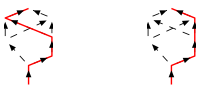

```mathematica
GraphicsRow[{
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnBC[#]]&/@domain[ΣnBC]]}}],
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnCUBE[#]]&/@domain[ΣnCUBE]]}}]},ImageSize->200,Spacings->150]
```

#### Points on the path.

```mathematica
PointsOnPath[Σn_,dt_]:=UnsortedUnion[Flatten[Table[Table[(1-t) NodePt[Σn[j]]+t NodePt[Σn[j+1]],{t,0,1,dt}],{j,1,nMax[Σn]-1}],1]];
position[point_,dt_]:=Position[AllPoints[dt],point][[1,1]];path[Σn_,dt_]:=position[#,dt]&/@PointsOnPath[Σn,dt]
```

#### Σpairs specifies the segments of the lattice to put points on. Probably you won’t heve much occasion to change it. Normally it is

```mathematica
Σpairs={{TRIV,MONO},{MONO,ORTH},{MONO,TRIG},{ORTH,TET},{TET,XISO},{TET,CUBE},{XISO,ISO},{TRIG,CUBE},{TRIG,XISO},{CUBE,ISO}};
```

#### Example

```mathematica
Graphics[{LatticeBlank,
{Blue,Thickness[.02],Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

## Densify the maps on the Σpairs segments.

#### The point command is set up so that point[ {0, {Σ_1, Σ_2} } ] = NodePt[Σ_1] point[ {1, {Σ_1, Σ_2} } ] = NodePt[Σ_2]

```mathematica
point[{t_,{Σ1_,Σ2_}}]:=(1-t) NodePt[Σ1]+t NodePt[Σ2];
UnsortedPointsWithTandΣpairs[dt__]:=DeleteDuplicates[Flatten[Table[{{t,#},point[{t,#}]},{t,0,1,dt}]&/@Σpairs,1],#1[[2]]==#2[[2]]&];
PointsWithTandΣpairs[dt_]:=Sort[UnsortedPointsWithTandΣpairs[dt],OrderedQ[{#1[[2]],#2[[2]]}]&];
AllPoints[dt_]:=#[[2]]&/@PointsWithTandΣpairs[dt];
```

```mathematica
point[{0,{Σ1,Σ2}}]== NodePt[Σ1]
point[{1,{Σ1,Σ2}}]== NodePt[Σ2]
```

True

True

#### Example.

```mathematica
dt=.5;
Graphics[{LatticeBlank,
{Blue,Thickness[.015],PointSize[.05],
Point/@AllPoints[dt],
Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

#### Examples.

```mathematica
dt=.5;
ColumnForm[UnsortedPointsWithTandΣpairs[dt]]
Length[%[[1]]]
```

{{0.,{TRIV,MONO}},{0.,0.5}}
{{0.5,{TRIV,MONO}},{0.,1.}}
{{1.,{TRIV,MONO}},{0.,1.5}}
{{0.5,{MONO,ORTH}},{0.6,1.75}}
{{1.,{MONO,ORTH}},{1.2,2.}}
{{0.5,{MONO,TRIG}},{-0.6,2.175}}
{{1.,{MONO,TRIG}},{-1.2,2.85}}
{{0.5,{ORTH,TET}},{1.2,2.5}}
{{1.,{ORTH,TET}},{1.2,3.}}
{{0.5,{TET,XISO}},{0.,3.5}}
{{1.,{TET,XISO}},{-1.2,4.}}
{{0.5,{TET,CUBE}},{1.2,3.5}}
{{1.,{TET,CUBE}},{1.2,4.}}
{{0.5,{XISO,ISO}},{-0.6,4.25}}
{{1.,{XISO,ISO}},{0.,4.5}}
{{0.5,{TRIG,CUBE}},{0.,3.425}}
{{0.5,{TRIG,XISO}},{-1.2,3.425}}
{{0.5,{CUBE,ISO}},{0.6,4.25}}

18

```mathematica
ColumnForm[PointsWithTandΣpairs[dt]]
Length[%[[1]]]
```

{{1.,{MONO,TRIG}},{-1.2,2.85}}
{{0.5,{TRIG,XISO}},{-1.2,3.425}}
{{1.,{TET,XISO}},{-1.2,4.}}
{{0.5,{MONO,TRIG}},{-0.6,2.175}}
{{0.5,{XISO,ISO}},{-0.6,4.25}}
{{0.,{TRIV,MONO}},{0.,0.5}}
{{0.5,{TRIV,MONO}},{0.,1.}}
{{1.,{TRIV,MONO}},{0.,1.5}}
{{0.5,{TRIG,CUBE}},{0.,3.425}}
{{0.5,{TET,XISO}},{0.,3.5}}
{{1.,{XISO,ISO}},{0.,4.5}}
{{0.5,{MONO,ORTH}},{0.6,1.75}}
{{0.5,{CUBE,ISO}},{0.6,4.25}}
{{1.,{MONO,ORTH}},{1.2,2.}}
{{0.5,{ORTH,TET}},{1.2,2.5}}
{{1.,{ORTH,TET}},{1.2,3.}}
{{0.5,{TET,CUBE}},{1.2,3.5}}
{{1.,{TET,CUBE}},{1.2,4.}}

18

#### Example. These are all the points: They should be the same as in the third entries of the previous paragraph.

```mathematica
dt=.5;
AllPoints[dt]
Length[%]
```

{{-1.2,2.85},{-1.2,3.425},{-1.2,4.},{-0.6,2.175},{-0.6,4.25},{0.,0.5},{0.,1.},{0.,1.5},{0.,3.425},{0.,3.5},{0.,4.5},{0.6,1.75},{0.6,4.25},{1.2,2.},{1.2,2.5},{1.2,3.},{1.2,3.5},{1.2,4.}}

18

#### Example.

{TRIV,MONO,ORTH,TET,XISO,ISO}

{6,7,8,12,14,15,16,10,3,5,11}

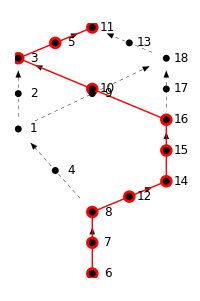

```mathematica
dt=.5;
Σn=ΣnBC;
Σn/@domain[Σn]
path[Σn,dt]
Graphics[{LatticeBlank,
{Red,PointSize[.045],
Point/@PointsOnPath[Σn,dt],
Line[NodePt[Σn[#]]&/@domain[Σn]]},
{PointSize[.025],Point/@AllPoints[dt]},
Text[Style[position[#,dt],12],#+{.25,0}]&/@AllPoints[dt]},ImageSize->200]
```

```mathematica
TandΣpair[pt_,dt_]:=Select[PointsWithTandΣpairs[dt],#[[2]]==pt &][[1,1]]   
TofPt[pt_,dt_]  :=TandΣpair[pt,dt][[1]];
Σ1ofPt[pt_,dt_]:=TandΣpair[pt,dt][[2,1]];
Σ2ofPt[pt_,dt_]:=TandΣpair[pt,dt][[2,2]];
NodePtsOfPt[pt_,dt_]:=NodePt/@TandΣpair[pt,dt][[2]];   (* points, not symmetry clases *)
dummy;
```

#### Example.

{-0.6,2.175}

{0.5,{MONO,TRIG}}

0.5

MONO

TRIG

{{0.,1.5},{-1.2,2.85}}

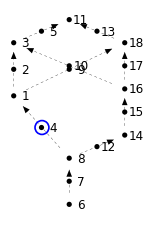

```mathematica
dt=.5;
pt=AllPoints[dt][[4]]  (* blue circle in diagram *)
TandΣpair[pt,dt]
TofPt[pt,dt]
Σ1ofPt[pt,dt]
Σ2ofPt[pt,dt]
NodePtsOfPt[pt,dt]
Graphics[{LatticeBlank,
{Blue,Thickness[.008],Circle[pt,.15]},
PointSize[.025],
Point/@AllPoints[dt],
Text[Style[position[#,dt],12],#+{.25,0}]&/@AllPoints[dt]},ImageSize->150]
```

#### Example. These are the points on the path:

```mathematica
dt=.5
Σn/@domain[Σn]
PointsOnPath[Σn,dt]
Length[%]
```

0.5

{TRIV,MONO,ORTH,TET,XISO,ISO}

{{0.,0.5},{0.,1.},{0.,1.5},{0.6,1.75},{1.2,2.},{1.2,2.5},{1.2,3.},{0.,3.5},{-1.2,4.},{-0.6,4.25},{0.,4.5}}

11

#### The main points figure, but still no elastic maps involved.

```mathematica
LatticeWithPtsText[dt_,Σn_]:=(Print["dt = ",dt];
Print["Σn values are ",Σn/@domain[Σn]];
Print["All points are ",AllPoints[dt]];
Print["Number of all points is ",Length[AllPoints[dt]]];
Print["path[Σn,dt] (red) is ",path[Σn,dt]];
Print["Points on red path are ",PointsOnPath[Σn,dt]];
Print["Number of points on red path is ",Length[PointsOnPath[Σn,dt]]];)
```

```mathematica
LatticeWithPts[dt_,Σn_]:=
Graphics[{LatticeBlank,
{Red,PointSize[.035],
Line[PointsOnPath[Σn,dt]],
Point/@PointsOnPath[Σn,dt]},  (* points on the red path *)
PointSize[.02],
Point/@AllPoints[dt],
Text[Style[position[#,dt],12],#+{.25,0}]&/@AllPoints[dt]},ImageSize->250]
```

#### Example

dt = 0.5

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

All points are {{-1.2,2.85},{-1.2,3.425},{-1.2,4.},{-0.6,2.175},{-0.6,4.25},{0.,0.5},{0.,1.},{0.,1.5},{0.,3.425},{0.,3.5},{0.,4.5},{0.6,1.75},{0.6,4.25},{1.2,2.},{1.2,2.5},{1.2,3.},{1.2,3.5},{1.2,4.}}

Number of all points is 18

path[Σn,dt] (red) is {6,7,8,12,14,15,16,10,3,5,11}

Points on red path are {{0.,0.5},{0.,1.},{0.,1.5},{0.6,1.75},{1.2,2.},{1.2,2.5},{1.2,3.},{0.,3.5},{-1.2,4.},{-0.6,4.25},{0.,4.5}}

Number of points on red path is 11

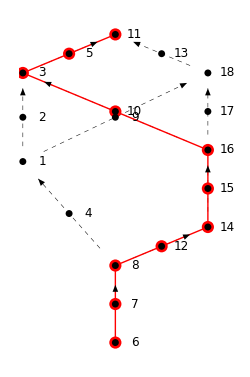

```mathematica
dt=.5;
Σn=ΣnBC;
LatticeWithPtsText[dt,Σn]
LatticeWithPts[dt,Σn]
```

#### Choose Σn

```mathematica
Σn=ΣnCUBE;
```

```mathematica
Σn=ΣnTRIG;
```

```mathematica
Σn=ΣnBC;
```

```mathematica
ListΣ=Σn/@domain[Σn]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### Choose dt

```mathematica
dt=0.2;
```

#### Lattice for future use:

dt = 0.2

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

All points are {{-1.2,2.85},{-1.2,3.08},{-1.2,3.31},{-1.2,3.54},{-1.2,3.77},{-1.2,4.},{-0.96,2.58},{-0.96,4.1},{-0.72,2.31},{-0.72,3.08},{-0.72,3.8},{-0.72,4.2},{-0.48,2.04},{-0.48,4.3},{-0.24,3.6},{-0.24,1.77},{-0.24,3.31},{-0.24,4.4},{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.,4.5},{0.24,4.4},{0.24,1.6},{0.24,3.4},{0.24,3.54},{0.48,4.3},{0.48,1.7},{0.72,3.2},{0.72,3.77},{0.72,4.2},{0.72,1.8},{0.96,1.9},{0.96,4.1},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{1.2,3.2},{1.2,3.4},{1.2,3.6},{1.2,3.8},{1.2,4.}}

Number of all points is 48

path[Σn,dt] (red) is {19,20,21,22,23,24,27,31,35,36,38,39,40,41,42,43,32,28,15,11,6,8,12,14,18,25}

Points on red path are {{0.,0.5},{0.,0.7},{0.,0.9},{0.,1.1},{0.,1.3},{0.,1.5},{0.24,1.6},{0.48,1.7},{0.72,1.8},{0.96,1.9},{1.2,2.},{1.2,2.2},{1.2,2.4},{1.2,2.6},{1.2,2.8},{1.2,3.},{0.72,3.2},{0.24,3.4},{-0.24,3.6},{-0.72,3.8},{-1.2,4.},{-0.96,4.1},{-0.72,4.2},{-0.48,4.3},{-0.24,4.4},{0.,4.5}}

Number of points on red path is 26

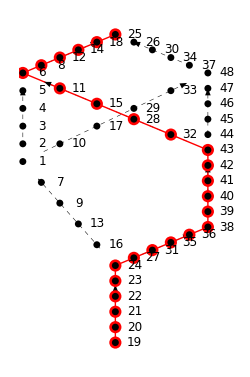

```mathematica
LatticeWithPtsText[dt,Σn]
LatticeWithPts[dt,Σn]
```

#### As functions of integer j. The integer j will give the point (j, 0) on the horizontal axis in the Beta curve diagrams. It runs over 1, 2, 3, ..., Length[path]. Not needed for the cumulative diagram or for the Lattice file.

```mathematica
PathPtOfJ[j_,Σn_,dt_]:=PointsOnPath[Σn,dt][[j]];  
jIsNode[j_,Σn_,dt_]:=xyIsNodePt[PathPtOfJ[j,Σn,dt]];  (* A statement, either true or false *)
JlistForNodes[Σn_,dt_]:=Select[Range[Length[PointsOnPath[Σn,dt]]],jIsNode[#,Σn,dt]&];
ΣofJ[j_,Σn_,dt_]:=If[TofPt[PathPtOfJ[j,Σn,dt],dt]==0.,
                                                             Σ1ofPt[PathPtOfJ[j,Σn,dt],dt],
                                                        If[TofPt[PathPtOfJ[j,Σn,dt],dt]==1.,
                                                          Σ2ofPt[PathPtOfJ[j,Σn,dt],dt]," "]]   (* The symmetry class Σ for the elastic map at n, but only if n is a node *)
```

#### Example

```mathematica
Print["dt = ",dt];
Print["Σn values are ",Σn/@domain[Σn]];
PathPtOfJ[4,Σn,dt]
jIsNode[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
JlistForNodes[Σn,dt]
ΣofJ[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
```

dt = 0.2

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

{0.,1.1}

{True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True}

{1,6,11,16,21,26}

{TRIV, , , , ,MONO, , , , ,ORTH, , , , ,TET, , , , ,XISO, , , , ,ISO}

## Section 2. Elastic maps at nodes. There is no dt at this stage.

#### Choose Tmat

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownNew;
```

#### Check for symmetry. Display output.

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatBrownNew

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

10-31-2023 8:30

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

#### SmatOfΣ[Σ, Tmat, Σn, pw] is the elastic map at node Σ. It should have symmetry Σ The input Σn is needed for pw = pw3. You can enter the command SmatOfΣ, but do not try to evaluate it unless you have run the appropriate OutputFor, described momentarily.

```mathematica
SmatOfΣ[Σ_,Tmat_,dummy_,pw2]:=Closest[Tmat,Σ];
SmatOfΣ[Σ_,Tmat_,Σn_,      pw3]:=ClosestToPrevious[Select[domain[Σn],Σn[#]==Σ &][[1]],Tmat,Σn]
SmatOfΣ[Σ_,Tmat_,dummy_,pw4]:=ProjToVSigOfU[Tmat,id,Σ]   (* We could make it depend on U *)
```

```mathematica
PreviousSmatOfΣ[Σ_,Tmat_,Σn_,pw3]:=ClosestToPrevious[Select[domain[Σn],Σn[#]==Σ &][[1]]-1,Tmat,Σn]
```

#### For pw2. Only run if you want pw2.

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,#]&/@ListSigmaAll
```

Tmat is TmatBrownNew

10-31-2023 8:30

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-31-2023 8:30

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-31-2023 8:30

NMinimize = {32.9751,{θ→1.47929,σ→-1.41812,ϕ→0.768554}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {84.8,-81.3,44.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.994223 | -0.0865168 | 0.0635195
0.0185598 | 0.721479 | 0.692188
-0.105714 | -0.68701 | 0.718917)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-31-2023 8:31

NMinimize = {40.302,{θ→0.0454989,σ→0.0274727,ϕ→1.66271}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,1.6,95.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0929013 | -0.0429475 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-31-2023 8:31

NMinimize = {94.1024,{θ→2.76397,σ→-0.686623,ϕ→3.00954}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {158.4,0.,172.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0 | -0.991294)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-31-2023 8:31

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

10-31-2023 8:31

NMinimize = {82.3728,{θ→0.22904,σ→-0.867254,ϕ→1.33736}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {13.1,-49.7,76.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

10-31-2023 8:32

NMinimize = {106.21,{θ→0.0974921,σ→-1.53454,ϕ→1.66977}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {5.6,-87.9,95.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.093709 | -0.101807 | 0.990381
-0.994946 | 0.0264644 | 0.0968614
-0.036071 | -0.994452 | -0.0988123)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

{Null,Null,Null,Null,Null,Null,Null,Null}

#### For pw3. This paragraph should be run for each path Σn that you want. ClosestToPrevious[n, Tmat, Σn] has symmetry Σn[n]. Save the output for comparison later.

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
OutputFor[Tmat,Σn[1]];   
OutputFor[ClosestToPrevious[#,Tmat,Σn],Σn[#+1]]&/@Range[nMax[Σn]-1]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

10-31-2023 8:32

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-31-2023 8:32

NMinimize = {19.3941,{θ→1.68223,σ→0.319894,ϕ→2.33199}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {96.4,0.,133.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0767049 | -0.993798 | -0.0805105
-0.68551 | -0.111201 | 0.719521
-0.724011 | 0 | -0.689788)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-31-2023 8:33

NMinimize = {26.7156,{θ→0.013398,σ→0.804573,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,46.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-31-2023 8:33

NMinimize = {23.9577,{θ→0.013398,σ→0.0191751,ϕ→1.67317}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {0.8,1.1,95.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133275
-0.994582 | 0.0190736 | -0.102194)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-31-2023 8:33

NMinimize = {88.7118,{θ→6.11108,σ→0.111619,ϕ→0.104147}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {350.1,0.,6.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.979889 | 0.171254 | 0.102423
-0.170326 | 0.985227 | -0.0178033
-0.103959 | 0 | 0.994582)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-31-2023 8:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 84.9089   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.31 = 17.77^o (Angle between T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null}

#### For pw4, no OutputFor is needed here. (But of course you need OutputFor later in order to get the beta curves.)

#### Example. Elastic maps at the nodes on the path. Each should be the 6x6 matrix P(T, 𝒱_Σ(U_0)) in the corresponding OutputFor above. But note that for pw = pw3 the above T refers to the map at the preceding node, not to the original Tmat.

```mathematica
pw=pw2;
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
Chop[MatrixForm[SmatOfΣ[Σn[#],Tmat,Σn,pw]],0.0001]&/@domain[Σn]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267),(47.2694 | -3.19958 | -1.00821 | -9.32212 | 11.7379 | -8.26656
-3.19958 | 62.3442 | 2.27011 | -5.04078 | -11.271 | 7.50877
-1.00821 | 2.27011 | 60.5007 | -2.56615 | -0.102698 | -2.19801
-9.32212 | -5.04078 | -2.56615 | 95.9546 | 48.8761 | 34.9099
11.7379 | -11.271 | -0.102698 | 48.8761 | 148.264 | -19.294
-8.26656 | 7.50877 | -2.19801 | 34.9099 | -19.294 | 189.267),(47.8734 | -0.0381235 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381235 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267),(50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

```mathematica
pw=pw3;
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
Chop[MatrixForm[SmatOfΣ[Σn[#],Tmat,Σn,pw]],0.0001]&/@domain[Σn]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267),(47.3087 | -3.09908 | -1.05627 | -9.84992 | 11.085 | -8.30133
-3.09908 | 62.1997 | 2.3175 | -4.94367 | -10.8641 | 7.22046
-1.05627 | 2.3175 | 60.4795 | -2.21162 | 0.294029 | -1.79801
-9.84992 | -4.94367 | -2.21162 | 95.826 | 48.9018 | 34.886
11.085 | -10.8641 | 0.294029 | 48.9018 | 148.519 | -19.3664
-8.30133 | 7.22046 | -1.79801 | 34.886 | -19.3664 | 189.267),(47.3843 | -0.315251 | -1.42524 | 2.43642 | 4.1673 | 0.0956792
-0.315251 | 62.0514 | 0.103913 | -5.15905 | -10.8992 | 7.14088
-1.42524 | 0.103913 | 60.4942 | -0.675366 | -0.859386 | -0.931263
2.43642 | -5.15905 | -0.675366 | 95.4268 | 48.601 | 34.7455
4.1673 | -10.8992 | -0.859386 | 48.601 | 148.977 | -19.6439
0.0956792 | 7.14088 | -0.931263 | 34.7455 | -19.6439 | 189.267),(54.1924 | -0.525618 | -2.42965 | 0.452524 | 2.92937 | -0.621951
-0.525618 | 57.1249 | 0.36547 | 2.27629 | -16.8528 | 3.5781
-2.42965 | 0.36547 | 77.5353 | 0.0029275 | 0.377316 | -0.0640492
0.452524 | 2.27629 | 0.0029275 | 77.5424 | 1.05256 | -0.178672
2.92937 | -16.8528 | 0.377316 | 1.05256 | 147.938 | -19.9506
-0.621951 | 3.5781 | -0.0640492 | -0.178672 | -19.9506 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

```mathematica
pw=pw4;
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
Chop[MatrixForm[SmatOfΣ[Σn[#],Tmat,Σn,pw]],0.0001]&/@domain[Σn]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267),(50. | -4.8 | 0 | 0 | 0 | 0
-4.8 | 53.8 | 0 | 0 | 0 | 0
0 | 0 | 67.2 | -5.5 | 6.63953 | -13.6355
0 | 0 | -5.5 | 94.1 | 48.151 | 36.9873
0 | 0 | 6.63953 | 48.151 | 149.233 | -18.4791
0 | 0 | -13.6355 | 36.9873 | -18.4791 | 189.267),(50. | 0 | 0 | 0 | 0 | 0
0 | 53.8 | 0 | 0 | 0 | 0
0 | 0 | 67.2 | 0 | 0 | 0
0 | 0 | 0 | 94.1 | 48.151 | 36.9873
0 | 0 | 0 | 48.151 | 149.233 | -18.4791
0 | 0 | 0 | 36.9873 | -18.4791 | 189.267),(51.9 | 0 | 0 | 0 | 0 | 0
0 | 51.9 | 0 | 0 | 0 | 0
0 | 0 | 67.2 | 0 | 0 | 0
0 | 0 | 0 | 94.1 | 0 | 0
0 | 0 | 0 | 0 | 149.233 | -18.4791
0 | 0 | 0 | 0 | -18.4791 | 189.267),(51.9 | 0 | 0 | 0 | 0 | 0
0 | 51.9 | 0 | 0 | 0 | 0
0 | 0 | 80.65 | 0 | 0 | 0
0 | 0 | 0 | 80.65 | 0 | 0
0 | 0 | 0 | 0 | 149.233 | -18.4791
0 | 0 | 0 | 0 | -18.4791 | 189.267),(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)}

## Section 3. Just for the cumulative diagram. None of the commands in this section is needed for the superlattice file.

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,Σn_,pw_]:=AngleMatrix[SmatOfΣ[Σn[n],Tmat,Σn,pw],SmatOfΣ[Σn[n+1],Tmat,Σn,pw]];
yy[1,   Tmat_,Σn_,pw_]:=0;
yy[n_,Tmat_,Σn_,pw_]:=yy[n-1,Tmat,Σn,pw]+AngleToNextFrom[n-1,Tmat,Σn,pw];
```

```mathematica
ydiff[n_,Tmat_,Σn_,pwA_,pwB_]:=yy[n,Tmat,Σn,pwA]-yy[n,Tmat,Σn,pwB];
dymax[Tmat_,Σn_,pwA_,pwB_]:=Max[ydiff[#,Tmat,Σn,pwA,pwB]&/@domain[Σn]];
```

#### Example.

```mathematica
MatrixNote[Tmat]
Σn/@domain[Σn]
yy[#,Tmat,Σn,pw2]/Degree&/@domain[Σn]
```

Tmat is TmatBrownNew

{TRIV,MONO,ORTH,TET,XISO,ISO}

{0,3.77222,8.99293,13.8115,31.7354,50.2722}

#### The Pathway 1 “curves” are just colored line segments (hues are set in chooseTmat.nb):

```mathematica
BetaSeg[i_,Tmat_]:={hue[ListΣ[[i]] ],Line[{{1,0},{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i]] ]]/Degree}}],Point[{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i]]  ]]/Degree}]}
```

#### Main plot

```mathematica
psz = 0.015;
pw2col=Gray;
pw3col=Magenta;
pw4col=Blue;
```

```mathematica
GraphicsForCumulative[Tmat_,Σn_,WantPW1_,WantPW2_,WantPW3_,WantPW4_]:=Graphics[{{
Dashing[{.01,.02}],Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,yy[nMax[Σn],Tmat,Σn,pw2]/Degree}}],{n,nMax[Σn]}]},     (* vertical dashed lines *)
If[WantPW2=="WantPW2",
{{Dashing[{.01,.02}],         (* horizontal dashed steps, pw2 only*)
Line[{{#,      yy[#,Tmat,Σn,pw2]/Degree},
   {#+1,yy[#,Tmat,Σn,pw2]/Degree}}]&/@Range[nMax[Σn]-1]},
{pw2col,PointSize[psz],Point[{#,yy[#,Tmat,Σn,pw2]/Degree}]&/@domain[Σn], (* pw2 *)
 Line[{#,yy[#,Tmat,Σn,pw2]/Degree}&/@domain[Σn]]}}],  
If[WantPW1=="WantPW1",
{PointSize[psz],BetaSeg[#,Tmat]&/@Range[2,nMax[Σn]]}],
If[WantPW3=="WantPW3",
{pw3col,PointSize[psz],
Point[{#,yy[#,Tmat,Σn,pw3]/Degree}]&/@domain[Σn], (* pw3 *)
Line[  {#,yy[#,Tmat,Σn,pw3]/Degree}  &/@domain[Σn]]}], 
If[WantPW4=="WantPW4",
{pw4col,PointSize[psz],
Point[{#,yy[#,Tmat,Σn,pw4]/Degree}]&/@domain[Σn], (* pw4 *)
Line[  {#,yy[#,Tmat,Σn,pw4]/Degree}  &/@domain[Σn]]}], 
Text[Style[Σn[#],14],{#,-3}]&/@domain[Σn],
Text[Style["cumulative angle for indicated nodes",14],{-.4,.5yy[nMax[Σn],Tmat,Σn,pw2]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

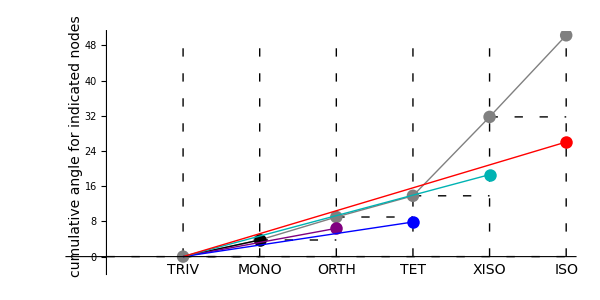

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
GraphicsForCumulative[Tmat,Σn,"WantPW1","WantPW2","noWantPW3","noWantPW4"]
```

Tmat is TmatBrownNew

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

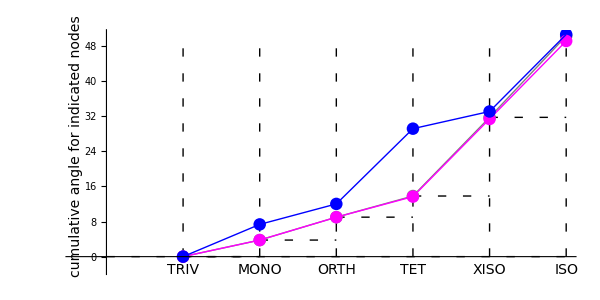

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]];
GraphicsForCumulative[Tmat,Σn,"noWantPW1","WantPW2","WantPW3","WantPW4"]
```

#### Difference between Pathways (3 vs 4 and 3 vs 2)

Tmat is TmatBrownNew

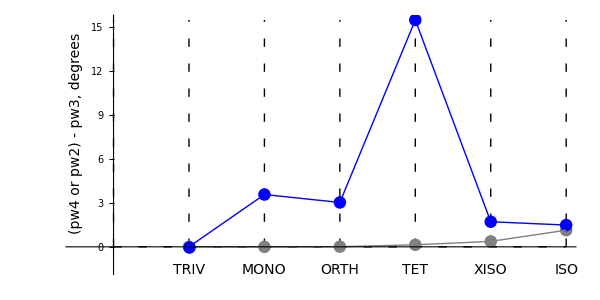

```mathematica
MatrixNote[Tmat]
Graphics[{
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,pw4,pw3]/Degree}}],{n,0,nMax[Σn]}]},
{pw2col,PointSize[psz],Point[{#,ydiff[#,Tmat,Σn,pw2,pw3]/Degree}]&/@domain[Σn]}, (* points *)
{pw2col,                                        Line[{#,ydiff[#,Tmat,Σn,pw2,pw3]/Degree}&/@domain[Σn]]},  (* line *)
{pw4col,PointSize[psz],Point[{#,ydiff[#,Tmat,Σn,pw4,pw3]/Degree}]&/@domain[Σn]}, (* points *)
{pw4col,                                        Line[{#,ydiff[#,Tmat,Σn,pw4,pw3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,pw4,pw3]/Degree}]&/@domain[Σn],
Text[Style["(pw4 or pw2) - pw3, degrees",14],{-.5,.5dymax[Tmat,Σn,pw4,pw3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```

## For Reference: Brown

-Graphics-

-Graphics-

-Graphics-

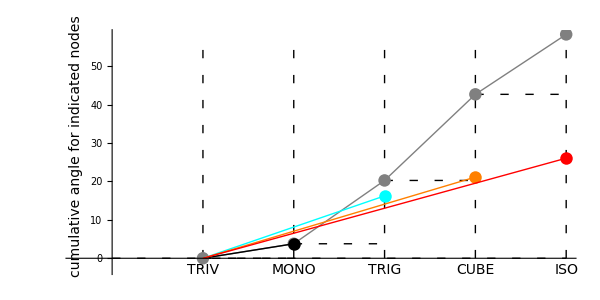

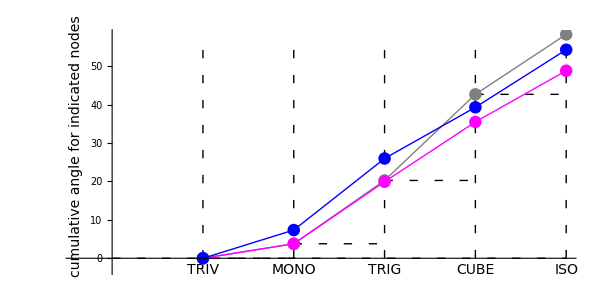

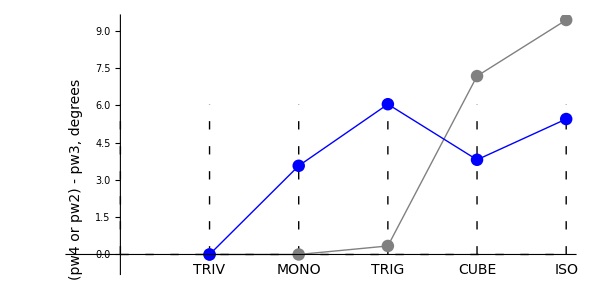

## For Reference: SSA2023

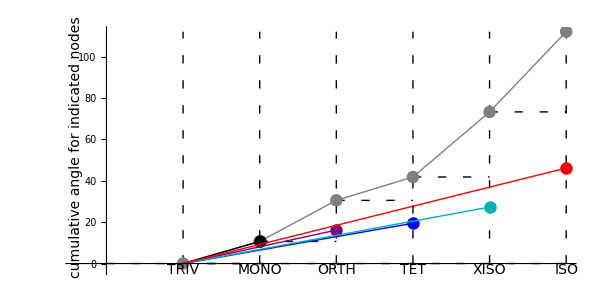

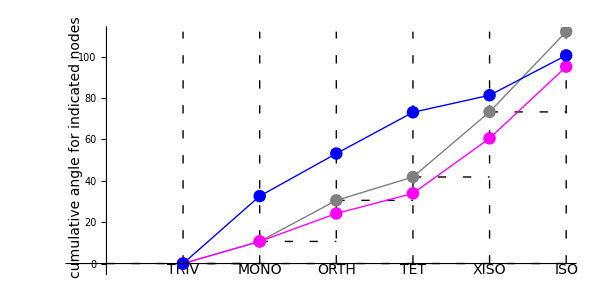

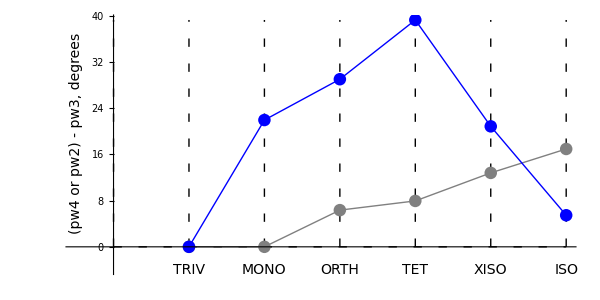

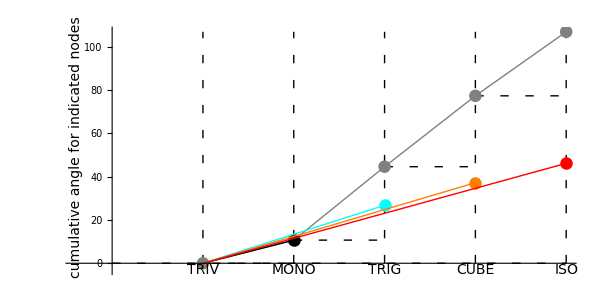

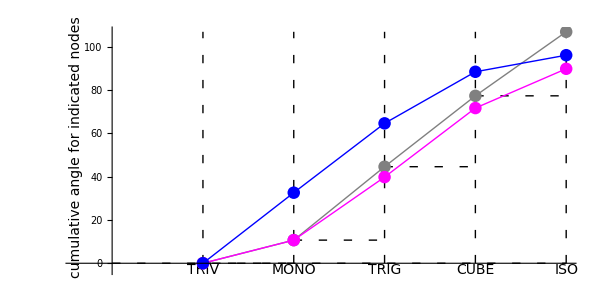

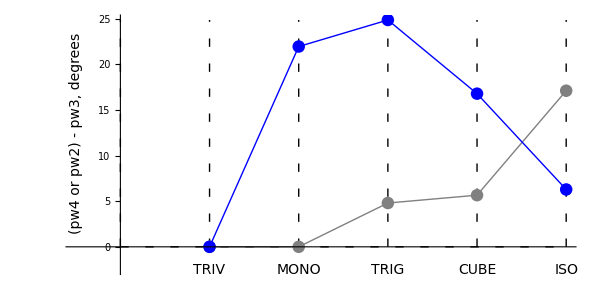

## For Reference: Igel

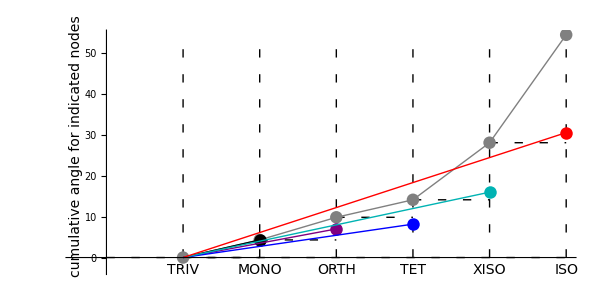

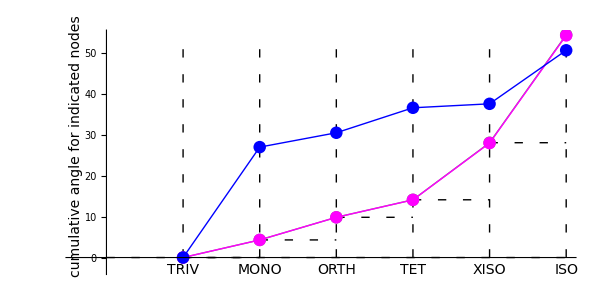

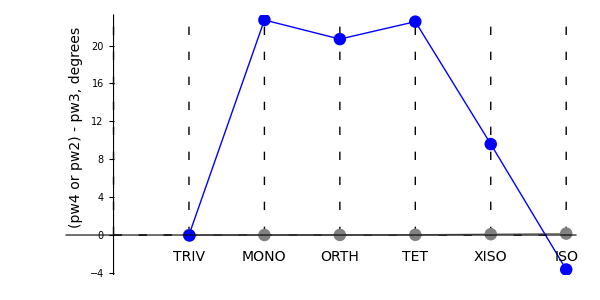

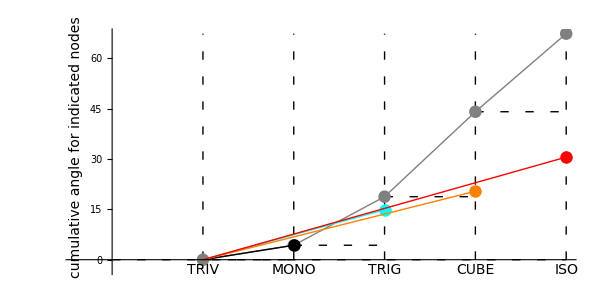

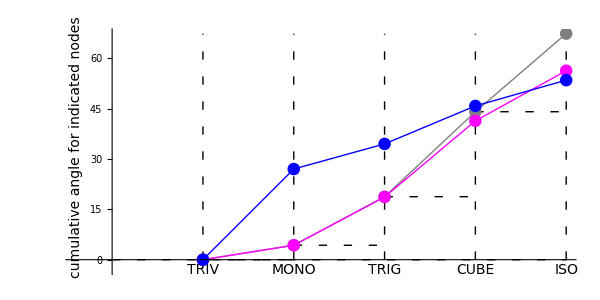

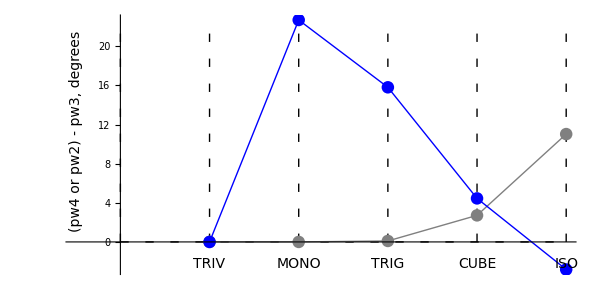

## For Reference: Mar17